### Basic:

```mathematica
FNJ=FileNameJoin;
```

```mathematica
RelativeDir[dir_]:=FileNameJoin[{NotebookDirectory[],dir}]
```

```mathematica
Replicate[list_,n_]:=Flatten[Transpose[ConstantArray[list,n]]]
```

```mathematica
ToText[list_]:=StringJoin[Riffle[ToString[#]&/@list,"\n"]]
```

```mathematica
ShiftLeft[list_,n_]:=Drop[PadLeft[list,Length[list]+n],-n]
```

```mathematica
ShiftRight[list_,n_]:=Drop[PadRight[list,Length[list]+n],n]
```

```mathematica
Half[list_]:= Take[list, Floor[Length[list]/2]]
```

### Before simulation:

```mathematica
(*-------parameters-------*)
td = 3; blocks = 4; l = 100;
(*------------------------*)
data=RandomInteger[{-16,16},l];
ker = RandomInteger[{-16,16},td*blocks];
upKer = RandomInteger[{-16,16},td*6];
```

```mathematica
expected=ListConvolve[Reverse[ker],data,1,0];
```

```mathematica
Max[Abs[expected]]
```

990

```mathematica
Export[RelativeDir["data.dat"],ToText[Replicate[data,td]]];Export[RelativeDir["coefs.dat"],ToText[ker]];Export[RelativeDir["upsamp_coefs.dat"],ToText[upKer]];
```

### After simulation:

```mathematica
ker
```

{12,14,11,5,5,-7,-5,-15,3,-16,13,-6}

```mathematica
expected
```

{-60,82,-104,96,-365,-130,-8,75,281,154,170,-117,-295,-671,-60,-521,990,117,643,325,68,246,-381,466,-71,446,-128,339,-200,-161,-236,-335,-308,-282,-68,-108,3,665,241,163,-59,-291,-219,-329,146,-41,-69,183,-394,-439,-419,250,84,850,336,313,5,-472,-87,-558,75,59,400,214,44,-370,-471,-632,-3,-442,602,259,520,152,325,-43,268,160,-331,-23,-599,-158,-337,202,49,404,-103,438,-159,327,-95,89,134,-262,-352,-376,-403,-455,-119,-40}

```mathematica
upKer
```

{-10,10,15,11,1,5,15,-6,-13,10,4,7,-3,0,14,11,10,-8}

```mathematica
Max[lol]
```

14568

```mathematica
upIn=Flatten@Riffle[expected,{ConstantArray[0,2]}]
```

{-60,0,0,82,0,0,-104,0,0,96,0,0,-365,0,0,-130,0,0,-8,0,0,75,0,0,281,0,0,154,0,0,170,0,0,-117,0,0,-295,0,0,-671,0,0,-60,0,0,-521,0,0,990,0,0,117,0,0,643,0,0,325,0,0,68,0,0,246,0,0,-381,0,0,466,0,0,-71,0,0,446,0,0,-128,0,0,339,0,0,-200,0,0,-161,0,0,-236,0,0,-335,0,0,-308,0,0,-282,0,0,-68,0,0,-108,0,0,3,0,0,665,0,0,241,0,0,163,0,0,-59,0,0,-291,0,0,-219,0,0,-329,0,0,146,0,0,-41,0,0,-69,0,0,183,0,0,-394,0,0,-439,0,0,-419,0,0,250,0,0,84,0,0,850,0,0,336,0,0,313,0,0,5,0,0,-472,0,0,-87,0,0,-558,0,0,75,0,0,59,0,0,400,0,0,214,0,0,44,0,0,-370,0,0,-471,0,0,-632,0,0,-3,0,0,-442,0,0,602,0,0,259,0,0,520,0,0,152,0,0,325,0,0,-43,0,0,268,0,0,160,0,0,-331,0,0,-23,0,0,-599,0,0,-158,0,0,-337,0,0,202,0,0,49,0,0,404,0,0,-103,0,0,438,0,0,-159,0,0,327,0,0,-95,0,0,89,0,0,134,0,0,-262,0,0,-352,0,0,-376,0,0,-403,0,0,-455,0,0,-119,0,0,-40}

```mathematica
lol=ListConvolve[Reverse[upKer],upIn,1,0]
```

{480,-600,-660,-1496,820,1082,1560,-1280,-1990,-870,1648,1288,2170,-4618,-4773,-2536,-810,567,-4849,-1400,-3872,2043,1476,-3830,51,4153,-4139,-2794,-1892,3701,-202,1066,6555,996,-2245,4863,2440,-2163,3457,3194,-5234,-6232,-6298,632,-3022,4431,-4541,-19673,-10141,12221,-287,2277,-4175,-12224,-168,6746,14857,-9154,-3343,12535,4121,-1670,24058,8335,9919,6784,7713,-3675,6529,3046,11991,6894,6442,-392,-4801,5903,9536,6090,2498,-2281,-3117,-3844,2256,16444,6287,-599,-3248,3690,250,5915,-123,-862,-4896,624,-3735,-2578,2300,132,-12748,-5138,-4905,-8839,-4800,-1748,-8993,-3273,-3055,-9749,-4911,-2208,-4591,-11180,3264,5184,4237,182,1138,5126,3484,7257,-5809,-4693,12360,2880,-3009,9506,6326,3487,-3680,2726,-1527,-7374,-1374,3901,-6241,576,-1293,-10075,-183,-1261,-3610,-9545,-1729,2571,1559,-7114,-1292,2159,-1825,-4763,-8891,-7343,-4836,-5937,2601,-3590,6377,3234,-16765,-6532,7635,4424,-2130,-2613,5517,2023,2086,19135,-186,-1122,13650,7179,-3794,11473,4484,6108,400,6482,-3825,-10439,1835,6369,-8526,-4482,-1542,-11703,-2110,2841,366,-769,498,-2399,-3318,-3819,11132,1294,-4435,3837,-1001,-4828,3389,2370,-3850,-10225,-3881,2490,-10053,4003,-4052,-22748,-10714,5629,-3043,-6924,-4502,-5664,-69,3937,10620,-2204,-1528,6900,-3819,-42,23246,9523,3337,4701,4038,6178,11737,6506,4830,1873,11228,-135,-31,-2154,2009,2637,768,-8436,-4052,1840,3154,-6056,-2665,-4359,-14809,-4733,1649,-4275,-1209,-739,-12166,-6526,722,5514,142,-3963,-952,-6800,2534,15494,4706,-2357,486,2318,6534,10863,4076,-277,-2219,2959,2560,7997,1033,3219,-967,5080,-2957,1368,3359,-343,-4726,-6476,-6473,-1761,907,-2842,-10171,642,-2864,-17058,-9041,-3518,-10866,-6452}

```mathematica
2^13
```

8192

```mathematica
Floor[lol/2^8]
```

{1,-3,-3,-6,3,4,6,-5,-8,-4,6,5,8,-19,-19,-10,-4,2,-19,-6,-16,7,5,-15,0,16,-17,-11,-8,14,-1,4,25,3,-9,18,9,-9,13,12,-21,-25,-25,2,-12,17,-18,-77,-40,47,-2,8,-17,-48,-1,26,58,-36,-14,48,16,-7,93,32,38,26,30,-15,25,11,46,26,25,-2,-19,23,37,23,9,-9,-13,-16,8,64,24,-3,-13,14,0,23,-1,-4,-20,2,-15,-11,8,0,-50,-21,-20,-35,-19,-7,-36,-13,-12,-39,-20,-9,-18,-44,12,20,16,0,4,20,13,28,-23,-19,48,11,-12,37,24,13,-15,10,-6,-29,-6,15,-25,2,-6,-40,-1,-5,-15,-38,-7,10,6,-28,-6,8,-8,-19,-35,-29,-19,-24,10,-15,24,12,-66,-26,29,17,-9,-11,21,7,8,74,-1,-5,53,28,-15,44,17,23,1,25,-15,-41,7,24,-34,-18,-7,-46,-9,11,1,-4,1,-10,-13,-15,43,5,-18,14,-4,-19,13,9,-16,-40,-16,9,-40,15,-16,-89,-42,21,-12,-28,-18,-23,-1,15,41,-9,-6,26,-15,-1,90,37,13,18,15,24,45,25,18,7,43,-1,-1,-9,7,10,3,-33,-16,7,12,-24,-11,-18,-58,-19,6,-17,-5,-3,-48,-26,2,21,0,-16,-4,-27,9,60,18,-10,1,9,25,42,15,-2,-9,11,10,31,4,12,-4,19,-12,5,13,-2,-19,-26,-26,-7,3,-12,-40,2,-12,-67,-36,-14,-43,-26}

```mathematica
result
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,-6,6,-7,-7,6,-4,0,5,7,-17,9,-25,-6,2,-3,2,-5,12,-27,0,-20,-35,39,-50,-4,-2,28,27,-16,19,-66,-8,-67,-51,61,-51,-10,7,42,42,-20,2,-59,-39,-78,-32,6,-4,-20,6,26,7,19,-27,-6,-4,-5,-16,-8,-4,-23,2,-18,-21,24,-28,-4,-9,17,14,-9,-5,-37,-21,-33,0,14,5,-22,-3,5,14,17,0,-36,13,-42,5,-6,22,5,-6,5,-53,-1,-60,7,25,4,3,-35,43,9,-4,-45,-37,-15,-18,28,3,43,4,-24,14,2,26,-35,-31,10,4,40,14,39,-14,-14,-37,5,-9,-7,0,-19,37,-20,11,-29,-11,36,-26,23,-10,33,53,-59,37,-12,-38,-38,-30,9,1,28,40,40,51,-15,35,57,-29,12,-29,-34,-13,14,28,10,30,0,49,68,-13,34,0,-22,-14,3,13,-3,37,-5,52,64,-28,63,-22,16,-70,-2,16,30,71,11,79,-10,-32,-34,20,30,-27,-17,-30,57,62,10,17,-27,-16,-44,49,-6,60,8,-22,25,-4,19,-46,27,13,35,50,-43,70,24,-16,-20,-47,23,-45,37,27,86,29,10,19,-33,23,-72,-23,40,-7,-4,-14,43,2,8,-47,-77,2,-59,-11,31,8,-16,-19,12,-14,12,-54,-75,5,-42,-7,27,4,-20,-17,-9,-16,0,-52,-41,-24,-22,26,-29,33,-1,-41,-11,6,-15,-12,25,-17,60,16,8,-1,19,10,1,48,-6,51,19,-31,4,36,-12,6,21,-24,44,39,-2,24,31,1,19,40,-1,26,52,-27,52,37,-10,20,-8,14,-13,45,26,55,36,-2,36,8,7,-27,-6,15,5,2,10,19,13,7,-6,-3,-4,-8,-8,-6,-2,-2,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
result=Flatten[Import[RelativeDir[FNJ[{"edit_firIP_v1_0.sim","sim_1","behav","xsim","out.dat"}]]]];
```

```mathematica
LongestCommonSubsequence[result,lol]
```

{-42}

### Random:

```mathematica
2224189. /2^16
```

33.9384

### Samples from fpga:

```mathematica
fker = Flatten@Import[RelativeDir["15l3.dat"]]
```

{-229,-211,135,1535,4358,8070,11299,12583,11299,8070,4358,1535,135,-211,-229}

```mathematica
fupker =  Flatten@Import[RelativeDir["20up2.dat"]]
```

{135,194,-360,-667,1157,1905,-3063,-5031,9293,29318,29318,9293,-5031,-3063,1905,1157,-667,-360,194,135}

```mathematica
2^14
```

16384

```mathematica
85*6229+960
```

530425

```mathematica
snaps=Reverse/@Import[RelativeDir["snap20.dat"]];
```

```mathematica
(*afirIn = snaps[[2]]*)
```

```mathematica
(*afirOut = snaps[[10]]*)
```

```mathematica
(*expafirOut=Floor[ListConvolve[fupker, Flatten[Riffle[Downsample[afirIn,3],{{0,0}}]]]/2^20]*)
```

```mathematica
(*LongestCommonSubsequence[afirOut,expafirOut]*)
```

```mathematica
snaps[[2]]
```

{-4350,-4118,-4022,-4308,-4300,-3796,-4202,-4350,-3486,-4022,-4308,-3121,-3796,-4202,-2666,-3486,-4022,-2165,-3121,-3796,-1690,-2666,-3486,-1190,-2165,-3121,-649,-1690,-2666,-124,-1190,-2165,417,-649,-1690,940,-124,-1190,1410,417,-649,1895,940,-124,2395,1410,417,2863,1895,940,3245,2395,1410,3559,2863,1895,3816,3245,2395,4021,3559,2863,4141,3816,3245,4177,4021,3559,4204,4141,3816,4100,4177,4021,3865,4204,4141,3490,4100,4177,2976,3865,4204,2295,3490,4100,1562,2976,3865,832,2295,3490,47,1562,2976,-739,832,2295,-1456,47}

```mathematica
firIn=Downsample[snaps[[2]],3,1]; firOut = Downsample[snaps[[3]],3,1]
```

{52252,45290,36679,26759,15945,4652,-6764,-17992,-28719,-38586,-47210,-54232,-59412,-62685,-64165,-64068,-62623,-60010,-56340,-51680,-46117,-39777,-32819,-25412,-17708,-9833,-1895,6014,13816,21444,28815,35808,42261,48004}

```mathematica
firOutExp=Floor[ListConvolve[fker,firIn]/2^12]
```

{-39777,-32819,-25412,-17708,-9833,-1895,6014,13816,21444,28815,35808,42261,48004,52889,56826,59762,61648,62384,61796,59665}

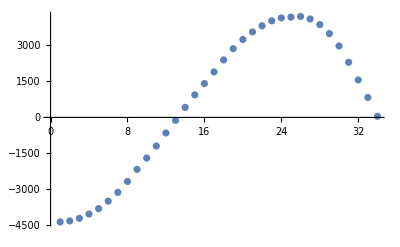

```mathematica
ListPlot[firIn]
```

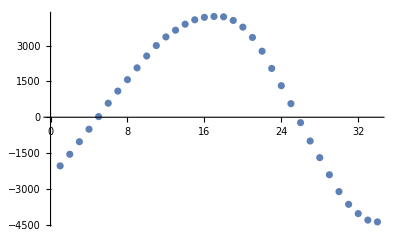

-Graphics-

```mathematica
firOut
```

{52252,45290,36679,26759,15945,4652,-6764,-17992,-28719,-38586,-47210,-54232,-59412,-62685,-64165,-64068,-62623,-60010,-56340,-51680,-46117,-39777,-32819,-25412,-17708,-9833,-1895,6014,13816,21444,28815,35808,42261,48004}

```mathematica
LongestCommonSubsequence[firOutExp,firOut]
```

{-39777,-32819,-25412,-17708,-9833,-1895,6014,13816,21444,28815,35808,42261,48004}

```mathematica
s
```

s

```mathematica
TableForm[Join[{Range[Length[snaps]]},Transpose@snaps]];
```

```mathematica
rng=Range[#,#+3]&/@Range[1,5*3,3];
```

```mathematica
(*(Drop[ShiftRight[snaps[[#1]],1]+(snaps[[#2]]*snaps[[#3]]),-4]==Drop[snaps[[#4]],4])&@@@rng*)
```

### Upsampling:

```mathematica
upker={0.004349354184333842,-0.012460526975242473,-0.04179305187785534,0.11580155515788863,0.4377645703903624,0.4377645703903624,0.11580155515788867,-0.04179305187785537,-0.012460526975242473,0.004349354184333842};
```

```mathematica
f=0.113;
```

```mathematica
in=Sin[2*π*f*#]&/@Range[100];
```

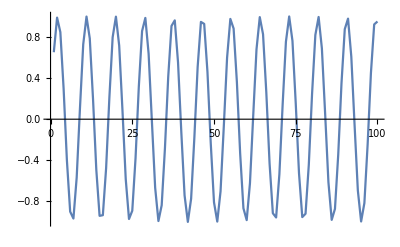

```mathematica
ListPlot[in,Joined->True]
```

```mathematica
inR=Append[Flatten@Riffle[in,0],0]
```

{0.651834,0,0.988652,0,0.847678,0,0.297042,0,-0.397148,0,-0.899405,0,-0.967001,0,-0.567269,0,0.106611,0,0.728969,0,0.999033,0,0.786288,0,0.193549,0,-0.492727,0,-0.940881,0,-0.934329,0,-0.476238,0,0.212007,0,0.797794,0,0.998027,0,0.715936,0,0.0878512,0,-0.58269,0,-0.971632,0,-0.891007,0,-0.379779,0,0.314987,0,0.857527,0,0.985645,0,0.637424,0,-0.0188484,0,-0.666012,0,-0.991308,0,-0.837528,0,-0.278991,0,0.414376,0,0.907484,0,0.962028,0,0.551646,0,-0.125333,0,-0.741742,0,-0.999684,0,-0.774503,0,-0.175023,0,0.509041,0,0.947098,0,0.927445,0,0.45958,0,-0.230389,0,-0.809017,0,-0.996666,0,-0.70265,0,-0.06906,0,0.597905,0,0.975917,0,0.882291,0,0.362275,0,-0.33282,0,-0.867071,0,-0.982287,0,-0.622788,0,0.0376902,0,0.679953,0,0.993611,0,0.827081,0,0.260842,0,-0.431456,0,-0.915241,0,-0.956712,0,-0.535827,0,0.144011,0,0.754251,0,0.99998,0,0.762443,0,0.156434,0,-0.525175,0,-0.952979,0,-0.920232,0,-0.442758,0,0.24869,0,0.819952,0,0.994951,0,0.689114,0,0.0502443,0,-0.612907,0,-0.979855,0,-0.873262,0,-0.344643,0,0.350534,0,0.876307,0,0.978581,0,0.60793,0,-0.0565185,0,-0.693653,0,-0.995562,0,-0.816339,0,-0.242599,0,0.448383,0,0.922673,0,0.951057,0}

```mathematica
out=ListConvolve[fupker/2^16,inR,1,0];
```

```mathematica
LinInt[list_]:=Module[{i,intlist={}},For[i=1,i< Length[list],i++,AppendTo[intlist,list[[i]]];AppendTo[intlist,(list[[i]]+list[[i+1]])/2]];AppendTo[intlist,Last[list]];AppendTo[intlist,2*Last[intlist]-intlist[[-2]]];intlist]
```

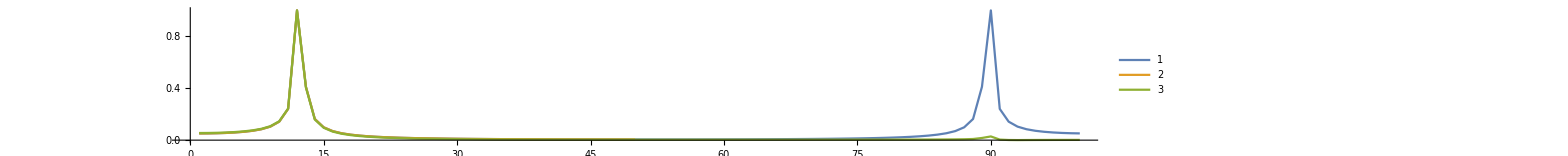

```mathematica
ListPlot[{Half@Abs@Fourier@inR/Max[Half@Abs@Fourier@inR],(Half@Abs@Fourier@in)/Max[Half@Abs@Fourier@in],(Half@Abs@Fourier@LinInt@in)/Max[Half@Abs@Fourier@LinInt@in]},Joined->True,PlotRange->All,ImageSize->5000, PlotLegends->Automatic,AspectRatio->0.1]
```

```mathematica
Manipulate[ListPlot[Abs@Fourier@Flatten@Riffle[Sin[2*π*f*#]&/@Range[100],{{0,0}}],Joined->True,ImageSize->300,PlotRange->{0,3}],{f,0,0.5,0.01}]
```

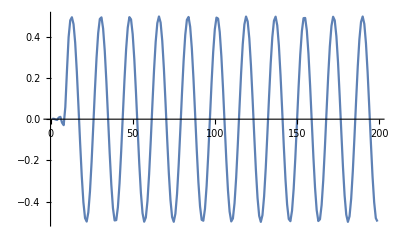

```mathematica
ListPlot[out,Joined->True]
```